```mathematica
Nt = 64; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 64;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];(*200 for Limits*)

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 8;
diffOrder = 6;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP3=NDSolve`FiniteDifferenceDerivative[Derivative[6],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);
LPX3 = LP3*((-1)^6)*(r*(Δx)^6);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;

gn3 = (LPX3[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX3 = Table[RotateRight[gn3,i],{i,-selectwidth,selectwidth}];
LPX3[[1,-1]]=0;
LPX3[[1,-2]]=0;
LPX3[[2,-1]]=0;
LPX3[[-1,1]]=0;
LPX3[[-1,2]]=0;
LPX3[[-2,1]]=0;
LPX3[[-3,1]] = 0;
LPX3[[-2,2]] = 0;
LPX3[[-1,3]] = 0;
LPX3[[1,-3]] = 0;
LPX3[[2,-2]] = 0;
LPX3[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/(4*10) + (ⅈ * LPX3)/(8*120)  ].(IP+(ⅈ * LPX)/4- LPX2/48-(ⅈ * LPX3)/(8*120)));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];*)
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)
MPtest = N[MP//.{N[r -> deltat / (deltax)^2,32]},32];

evalsPI = Eigenvalues[N[MPtest]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

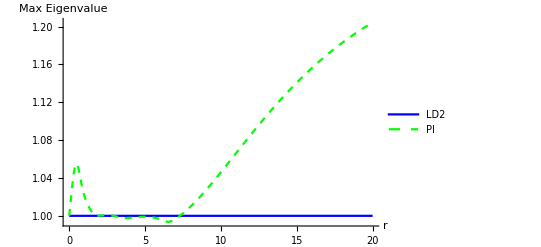

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

```mathematica
(*ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"},PlotRange->{All,{.99,1.02}}, AxesLabel->{"r", "Max Eigenvalue"}]*)
```

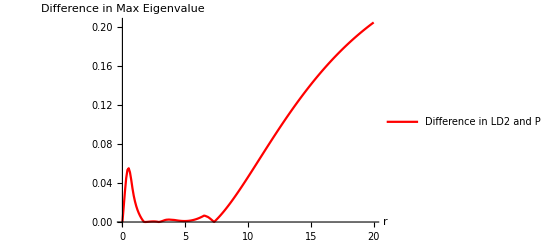

```mathematica
ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Red}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
Abs[maxevalsLD2 - maxevalsPI]
```

{0,0.0152086,0.0311346,0.0448797,0.0533373,0.0550469,0.0509558,0.0433605,0.0344917,0.0269751,0.0210844,0.0162831,0.0123803,0.00915443,0.00641937,0.00406604,0.00204882,0.000330642,0.0000191312,0.0000747495,0.000190079,0.000313504,0.00043006,0.000524783,0.000583924,0.00059576,0.000551065,0.000443286,0.000268522,0.0000253598,0.000285387,0.000660977,0.00109706,0.001588,0.00203685,0.00231726,0.00241054,0.00250225,0.0024009,0.00230023,0.00220365,0.00211442,0.00194638,0.00173068,0.00153532,0.00136445,0.00122185,0.00111094,0.00103477,0.000996044,0.000997112,0.00104001,0.00112646,0.00125789,0.00143546,0.00166007,0.0019324,0.00225289,0.00262181,0.00303922,0.00350503,0.00401902,0.00458081,0.00518991,0.00584574,0.0065476,0.00626065,0.00571952,0.00519822,0.00434566,0.00332708,0.00225035,0.00111723,0.0000704856,0.00131095,0.0026023,0.00394265,0.00533009,0.00676274,0.00823867,0.00975601,0.0113129,0.0129074,0.0145377,0.0162019,0.0178984,0.0196253,0.0213808,0.0231634,0.0249712,0.0268028,0.0286564,0.0305307,0.0324239,0.0343348,0.0362618,0.0382036,0.0401588,0.0421261,0.0441043,0.0460922,0.0480885,0.0500921,0.052102,0.0541171,0.0561363,0.0581587,0.0601834,0.0622093,0.0642357,0.0662617,0.0682866,0.0703094,0.0723296,0.0743463,0.076359,0.0783669,0.0803695,0.0823661,0.0843563,0.0863394,0.088315,0.0902826,0.0922417,0.0941918,0.0961327,0.0980638,0.0999848,0.101895,0.103795,0.105684,0.107561,0.109427,0.111281,0.113122,0.114952,0.116768,0.118572,0.120363,0.122141,0.123905,0.125656,0.127394,0.129118,0.130828,0.132524,0.134206,0.135874,0.137528,0.139168,0.140793,0.142404,0.144001,0.145584,0.147152,0.148706,0.150246,0.151771,0.153281,0.154778,0.15626,0.157727,0.159181,0.16062,0.162045,0.163455,0.164852,0.166234,0.167602,0.168957,0.170297,0.171623,0.172936,0.174235,0.17552,0.176792,0.17805,0.179294,0.180525,0.181743,0.182948,0.184139,0.185317,0.186483,0.187635,0.188775,0.189902,0.191016,0.192118,0.193207,0.194284,0.195349,0.196401,0.197441,0.19847,0.199486,0.200491,0.201484,0.202465,0.203435,0.204394}

```mathematica
(*MP//MatrixForm*)
```

```mathematica
maxevalsPI
```

{1,1.01521,1.03113,1.04488,1.05334,1.05505,1.05096,1.04336,1.03449,1.02698,1.02108,1.01628,1.01238,1.00915,1.00642,1.00407,1.00205,1.00033,0.999981,1.00007,1.00019,1.00031,1.00043,1.00052,1.00058,1.0006,1.00055,1.00044,1.00027,1.00003,0.999715,0.999339,0.998903,0.998412,0.997963,0.997683,0.997589,0.997498,0.997599,0.9977,0.997796,0.997886,0.998054,0.998269,0.998465,0.998636,0.998778,0.998889,0.998965,0.999004,0.999003,0.99896,0.998874,0.998742,0.998565,0.99834,0.998068,0.997747,0.997378,0.996961,0.996495,0.995981,0.995419,0.99481,0.994154,0.993452,0.993739,0.99428,0.994802,0.995654,0.996673,0.99775,0.998883,1.00007,1.00131,1.0026,1.00394,1.00533,1.00676,1.00824,1.00976,1.01131,1.01291,1.01454,1.0162,1.0179,1.01963,1.02138,1.02316,1.02497,1.0268,1.02866,1.03053,1.03242,1.03433,1.03626,1.0382,1.04016,1.04213,1.0441,1.04609,1.04809,1.05009,1.0521,1.05412,1.05614,1.05816,1.06018,1.06221,1.06424,1.06626,1.06829,1.07031,1.07233,1.07435,1.07636,1.07837,1.08037,1.08237,1.08436,1.08634,1.08832,1.09028,1.09224,1.09419,1.09613,1.09806,1.09998,1.1019,1.1038,1.10568,1.10756,1.10943,1.11128,1.11312,1.11495,1.11677,1.11857,1.12036,1.12214,1.12391,1.12566,1.12739,1.12912,1.13083,1.13252,1.13421,1.13587,1.13753,1.13917,1.14079,1.1424,1.144,1.14558,1.14715,1.14871,1.15025,1.15177,1.15328,1.15478,1.15626,1.15773,1.15918,1.16062,1.16204,1.16346,1.16485,1.16623,1.1676,1.16896,1.1703,1.17162,1.17294,1.17423,1.17552,1.17679,1.17805,1.17929,1.18053,1.18174,1.18295,1.18414,1.18532,1.18648,1.18764,1.18877,1.1899,1.19102,1.19212,1.19321,1.19428,1.19535,1.1964,1.19744,1.19847,1.19949,1.20049,1.20148,1.20247,1.20344,1.20439}